### Settings

```mathematica
d=4;
a=2;
delta = 1;
rMax=12; 
Z = 1 ;
```

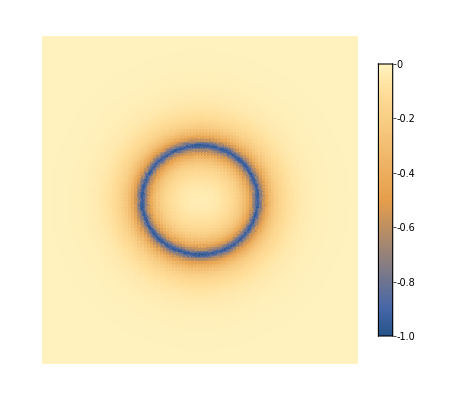

```mathematica
V[r_, θ_] := (-Z)/(Abs[r-0.1*d*Cos[θ]^2 -d]+delta) *Exp[-Abs[r-0.1*d*Cos[θ]^2 -d]/a]; 
DensityPlot[V[r ,θ]/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-rMax,rMax},{y,-rMax,rMax}, PlotTheme->"Minimal", PlotPoints->100,  PlotLegends->Automatic, PlotRange->All]
(*Export[NotebookDirectory[]<>"Coulomb.png",%,ImageResolution->100];*)
```

### 2 D Problem

```mathematica
{egnVal,egnVec}=NDEigensystem[
{(-1/2)* Laplacian[R2D[r,θ],{r,θ},"Polar"]+V[r,θ]*R2D[r,θ],
DirichletCondition[R2D[r,θ]==0,r==rMax*Sqrt[2]&&0<θ<=2*Pi],
PeriodicBoundaryCondition[R2D[r,θ],θ==0,TranslationTransform[{0,2 π}]]},
R2D[r,θ],{r,0,rMax*Sqrt[2]},{θ,0,2 π},10, Method -> {"Eigensystem" ->"Direct"} ];
ord =Ordering[egnVal];
Sort[Re[egnVal]]
```

{0.0032633,0.0204688,0.0207884,0.0415626,0.0416484,0.0611291,0.0618321,0.0665865,0.0690409,0.0691006}

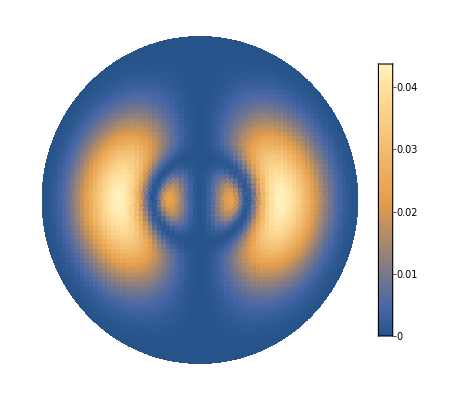

```mathematica
F1 =Part[Re[egnVec],Part[ord,2]]^2;
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y],{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal",  PlotPoints->100, PlotRange->All];
DensityPlot[F1/.r->Sqrt[x^2+y^2]/.θ->ArcTan[x,y]+2π,{x,-2rMax,2rMax},{y,-2rMax,2rMax}, PlotTheme->"Minimal", PlotPoints->100,PlotRange->All,  PlotLegends->Automatic];
Show[{%,%%}]
(*Export[NotebookDirectory[]<>"1.png",%,ImageResolution->400];*)
```

```mathematica
ParametricPlot3D[{r Cos[θ],r Sin[θ],1000*Evaluate[F1]},{r,0,rMax*Sqrt[2]},{θ,0,2 π}, PlotTheme->"Minimal", PlotPoints->100]
```

-Graphics3D-